```mathematica
data = Import["C:\\Documents and Settings\\Administrator\\桌面\\B站分析\\article-fans.txt","Table"];
```

```mathematica
data=Select[data,#⟦2⟧<500&];
```

```mathematica
article=data⟦;;,2⟧;
```

```mathematica
统计投稿数
```

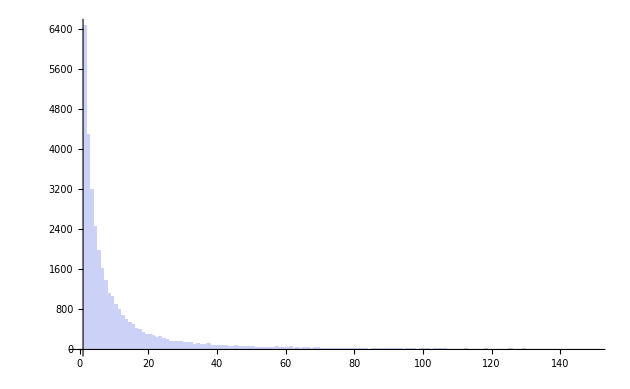

```mathematica
Histogram[Select[article,150> #&],{1}]
```

```mathematica
投稿数大于150的Up人数
```

```mathematica
Select[article,#>150&]//Length
```

571

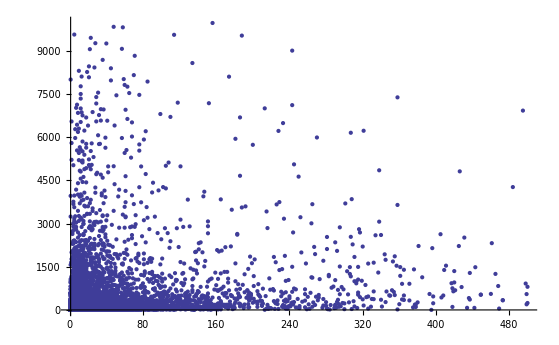

```mathematica
ListPlot[Select[data⟦;;,{2,3}⟧,#⟦2⟧<10000&&#⟦1⟧≤500&],PlotRange->All]
```

```mathematica
不同投稿数的平均好友数
```

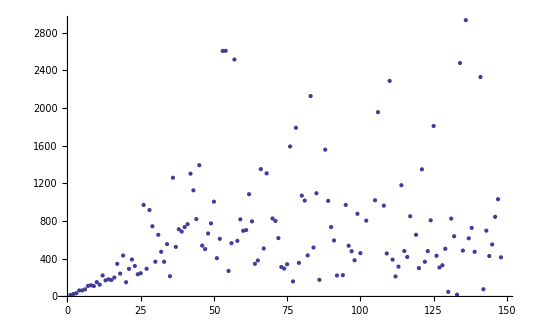

```mathematica
clu = Gather[data⟦;;,{2,3}⟧,#1⟦1⟧==#2⟦1⟧&];
articleFans=SortBy[{#⟦1,1⟧,N@Mean@#⟦;;,2⟧}&/@clu,First];
ListPlot@Select[articleFans,#⟦1⟧<150&]
```

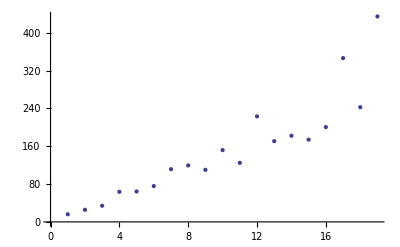

```mathematica
ListPlot@Select[articleFans,#⟦1⟧<20&]
```

```mathematica
每投一稿，平均水平涨17粉
```

```mathematica
FindFit[Select[articleFans,#⟦1⟧<20&],a x+b,{a,b},x]
```

{a→17.3422,b→-22.2525}

```mathematica
ID对应粉丝数
```

```mathematica
idfans = data⟦;;,{1,3}⟧;
```

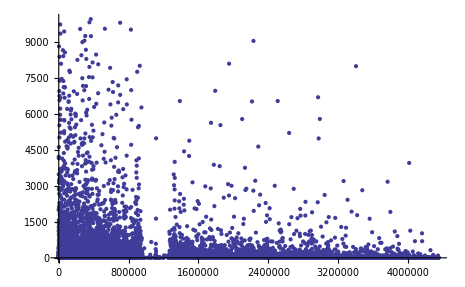

```mathematica
ListPlot[Select[idfans,#⟦2⟧<10000&],PlotRange->All]
```

```mathematica
idarticle = data⟦;;,{1,2}⟧;
```

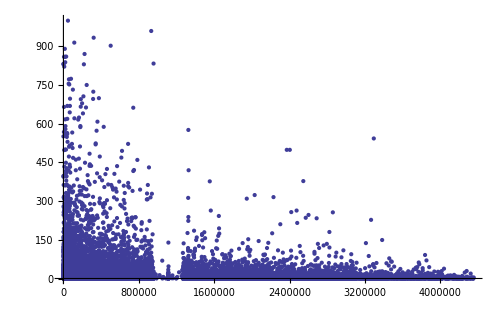

```mathematica
ListPlot[Select[idarticle,#⟦2⟧<1000&],PlotRange->All]
```

```mathematica
不同id段Up主统计
```

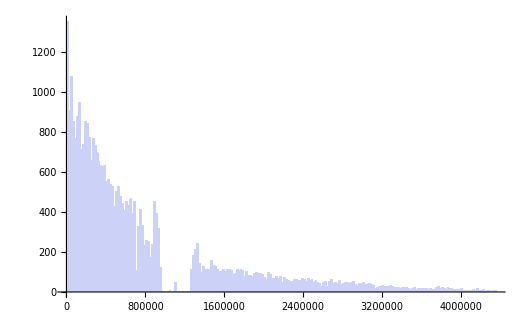

```mathematica
Histogram[data⟦;;,1⟧,200]
```

```mathematica
按ID聚类:
```

```mathematica
k=5000;
idclu = SortBy[Gather[data,Floor[#1⟦1⟧/k]==Floor[#2⟦1⟧/k]&],First];
idMeanArticle={#⟦1,1⟧,N@Mean@#⟦;;,2⟧}&/@idclu;
idMeanFans={#⟦1,1⟧,N@Mean@#⟦;;,3⟧}&/@idclu;
idMeanNumber={#⟦1,1⟧,N@Length@#}&/@idclu;
```

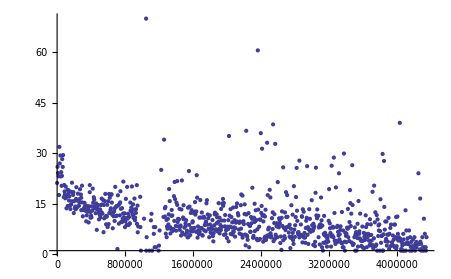

```mathematica
ListPlot[idMeanArticle,PlotRange->All]
```

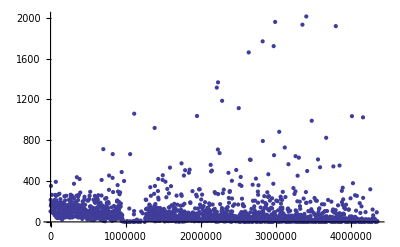

```mathematica
ListPlot[Select[idMeanFans,#⟦2⟧<10000&],PlotRange->All]
```

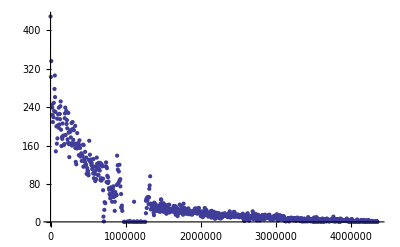

```mathematica
ListPlot[idMeanNumber,PlotRange->All]
```